```mathematica
Llist[g_,L_] := Table [ - g^2/(2) ,2 L] 
 Ldown[g_,L_] := DiagonalMatrix[Llist[g,L],1]
Lup[g_,L_] := DiagonalMatrix[Llist[g,L],-1]
LzLz[g_,L_] := DiagonalMatrix[Table[m^2 /2 ,{m,-L, L }] ]
FluxPlaqOperator[g_,L_]  := LzLz[g,L]+  Ldown[g,L]+  Lup[g,L]
```

```mathematica
Lp[L_]:=DiagonalMatrix[Table[Sqrt[m(2L-m+1)], {m, 1,2L}], 1]/Sqrt[2(2L-1)]
Lm[L_]:=DiagonalMatrix[Table[Sqrt[m(2L-m+1)], {m, 1,2L}], -1]/Sqrt[2(2L-1)]
Hqubit[g_, L_]:=  LzLz[g,L]-(g^2/2)(Lp[L]+Lm[L])
```

```mathematica
FluxPlaqOperator[1,2]//MatrixForm
Hqubit[1, 2]//MatrixForm
```

(2 | -1/2 | 0 | 0 | 0
-1/2 | 1/2 | -1/2 | 0 | 0
0 | -1/2 | 0 | -1/2 | 0
0 | 0 | -1/2 | 1/2 | -1/2
0 | 0 | 0 | -1/2 | 2)

(2 | -1/(√6) | 0 | 0 | 0
-1/(√6) | 1/2 | -1/2 | 0 | 0
0 | -1/2 | 0 | -1/2 | 0
0 | 0 | -1/2 | 1/2 | -1/(√6)
0 | 0 | 0 | -1/(√6) | 2)

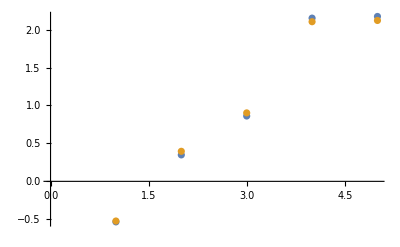

```mathematica
ListPlot[{Sort[Eigenvalues[FluxPlaqOperator[1,2]//N], Less], Sort[Eigenvalues[Hqubit[1, 2]//N], Less]}]
```

```mathematica
Uclock=Lp[2];
Uclock[[5, 1]] = 1;
Eigenvalues[Uclock]//FullSimplify
```

{Root0.285+0.877 ⅈRoot[-2+3 #1^5&,5]0.2849470152954436,Root0.285-0.877 ⅈRoot[-2+3 #1^5&,4]0.2849470152954436,(2/3)^(1/5),Root-0.746+0.542 ⅈRoot[-2+3 #1^5&,3]-0.7460009710363075,-(-2/3)^(1/5)}